## Nonlinear Magnetostatic Problem

David Meeker
dmeeker@ieee.org

May 30, 2004

The objective of this worksheet is to compare calculations of Force versus Position for a solenoid plunger with
experimental results from Roter's "Electromagnetic Devices." In particular, we will consider the device pictured
in Chapter IX, Figure 7.

First, load up the MathFEMM package:

```mathematica
<<c:\femm42\mathfemm\mathfemm.m
```

MathFEMM loaded at Sun 15 Nov 2015 21:06:00

and then start up a FEMM process with which to interact:

```mathematica
OpenFEMM[]
```

The actuator geometry was previously drawn in FEMM in the usual interactive mode. All components of the moving plunger were defined to be members of Group Number 1 so that the plunger can be selected with a single command and then moved with a second command.

```mathematica
OpenDocument[NotebookDirectory[]<>"roters1b.fem"]
```

We can set the coil current to investigate the 1.5A curve from Roters

```mathematica
MISetCurrent["Coil Current",1.5]
```

Then geometry can be saved to a temporary file name so that we don't overwrite our original geometry during the following analysis

```mathematica
MISaveAs[NotebookDirectory[]<>"temp.fem"]
```

The finished input geometry can be programmatically grabbed from FEMM for display in the Notebook. The FEMM model used to analyze this problem looks like:

```mathematica
Show[MIGetView[]]
```

-Graphics-

This loop repeatedly analyzes the problem, computes force on the plunger via the "Weighted Stress Tensor", then moves the plunger 1/10 of an inch.

```mathematica
data={};
```

```mathematica
For[i=0,i≤15,i++,
MIAnalyze[];
If[i==0,MILoadSolution[],MOReload[]];
MOGroupSelectBlock[1];
data=Append[data,{i/10.,MOBlockIntegral[19]}];
MISelectGroup[1];
MIMoveTranslate[0,-0.1];
MIClearSelected[];
]
```

The following data points were stripped from the figure in Roters using WinDig, a free and very useful tool for recovering numerical data from graphs.  See http://www.unige.ch/sciences/chifi/cpb/windig.html
A similar program that will run on 64-bit machines is ScanIt -- see http://www.amsterchem.com/scanit.html

```mathematica
rotersdata= {{0., 10.468}, {0.10552, 11.788},{0.203,12.584}, {0.30032, 13.144}, {0.40584, 13.698}, {0.50325, 14.759}, {0.60065, 16.075}, {0.698050, 17.647}, {0.79545, 19.985}, {0.90909, 21.563}, {1.0146, 23.138}, {1.1039, 23.94}, {1.2094, 23.728}, {1.3068, 23.002}, {1.4042, 21.254}, {1.5016, 18.486}};
```

```mathematica
rotersplot=ListPlot[rotersdata,PlotStyle->{PointSize[0.015]}];
```

```mathematica
feaplot=ListPlot[data.{{1,0},{0,1/4.4482}},Joined->True];
```

A combined plot compares the data from Roters to that produced from the finite element analysis. The solid line is the FEA results and the dots are the forces from Roters. There is a reasonable agreement between the two results.

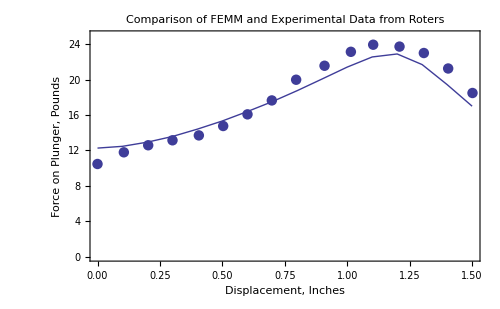

```mathematica
Show[rotersplot,feaplot,PlotRange->{0,25},Frame->True,FrameLabel->{"Displacement, Inches","Force on Plunger, Pounds"},PlotLabel->"Comparison of FEMM and Experimental Data from Roters",ImageSize->500,BaseStyle->{FontFamily->"Tahoma",FontSize->14}]
```

Now that we are done with the computation, we can shut down FEMM.

```mathematica
CloseFEMM[]
```